```mathematica
Itau[T_,Delta_]:=Delta (Exp[1/T]-1)
```

```mathematica
betapSHS[n_,T_,Delta_]:=(√(1+4Itau[T,Delta]n/(1-n))-1)/(2Itau[T,Delta])
```

```mathematica
betapSeed1[n_,T_,Delta_]:=If[T>0,betapSHS[n,T,Delta],n/(1-n)]
```

```mathematica
betapSeed2[n_,T_,Delta_]:=If[T>0,2betapSHS[n,T,Delta],If[n(1+Delta)<1,n/(1-n(1+Delta)),100]]
```

```mathematica
betap[n_,T_,Delta_]:=betap[n,T,Delta]=FindRoot[1/xi+(1-(1-Exp[-1/T])(1+Delta)Exp[-xi Delta])/(1-(1-Exp[-1/T])Exp[-xi Delta])==1/n,{xi,betapSeed1[n,T,Delta ], betapSeed2[n,T,Delta ]}][[1,2]]
```

```mathematica
Num[k_,xi_,T_,Delta_]:=B[xi,T,Delta]^2k^2-2A[xi,T,Delta](1-Cos[Delta k])
```

```mathematica
Den[k_,xi_,T_,Delta_]:=B[xi,T,Delta]^2(k^2+xi^2)-2B[xi,T,Delta](xi Cos[k]-k Sin[k]-A[xi,T,Delta](xi Cos[(1+Delta)k]-k Sin[(1+Delta)k]))+(1+A[xi,T,Delta]^2-2A[xi,T,Delta]Cos[Delta k])
```

```mathematica
A[xi_,T_,Delta_]:=(1-Exp[-1/T])Exp[-Delta xi]
```

```mathematica
B[xi_,T_,Delta_]:=(1-A[xi,T,Delta])/xi
```

```mathematica
Sk[k_,xi_,T_,Delta_]:=Num[k,xi,T,Delta]/Den[k,xi,T,Delta]
```

```mathematica
S[k_,n_,T_,Delta_]:=Sk[k,betap[n,T,Delta],T,Delta]
```

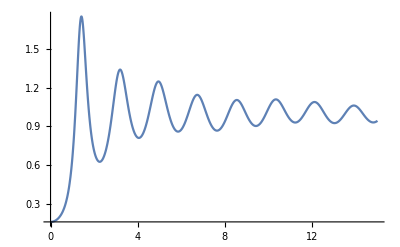

```mathematica
Plot[S[k,0.2,-0.3,2.5],{k,0,15},PlotRange->All]
```

```mathematica
betap[0.9,0.1,0.5]
```

8.43159

```mathematica
betapSeed1[0.9,0.1,0.5]
```

0.028542

```mathematica
betapSeed2[0.9,0.1,0.5]
```

0.0570839

```mathematica
betapSHS[0.9,0.1,0.5]
```

0.028542